```mathematica
(*tast #1:导入数据、处理数据并绘制散点图*)dataDSi=Import["D:\\Specific Heat of Degenerate Silicon.DAT"]
Print["length of the data: ",dataDSi//Length]
```

{{1.27,0.089},{1.98,0.167},{2.32,0.218},{3.08,0.401},{3.5,0.528},{4.17,0.788}}

length of the data: 6

```mathematica
dataDSi//MatrixForm
```

(1.27 | 0.089
1.98 | 0.167
2.32 | 0.218
3.08 | 0.401
3.5 | 0.528
4.17 | 0.788)

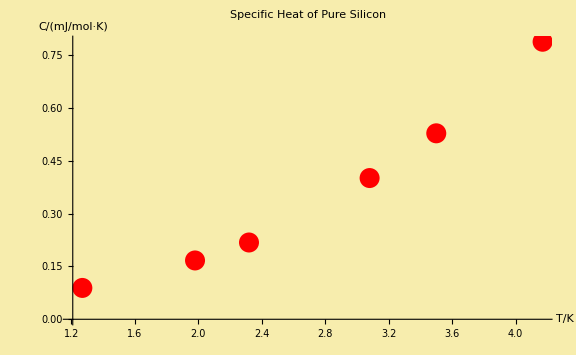

```mathematica
ListPlot[dataDSi,PlotStyle->{Red,PointSize[0.025]},PlotLabel->"Specific Heat of Pure Silicon",AxesLabel->{"T/K","C/(mJ/mol·K)"},LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0],Bold},Background->RGBColor[0.97,0.93,0.68],ImageSize->Large]
```

```mathematica
(*tast #3:  分析数据的机理模型 
C(T)=α T^3 式中，α=；
C(T)=α T^3+γ T 式中，α= ；γ=；
3.1 导入纯净硅的热容数据，提取3个数据点并与机理模型进行比较！
将数据和机理模型绘制于一副图片；
3.2 导入重掺杂硅的热容数据，提取3个数据点并与机理模型进行比较！
将数据和机理模型绘制于一副图片；*)
```